## Physical Parameters

```mathematica
Nt=4;Nxyz=4;
```

```mathematica
κ=0.12314361007807304879;
```

```mathematica
am[κ_]:=am[κ]=1/(2. κ)-4
```

```mathematica
am[κ]
```

0.0603

## Lattice Quantities

### Allowed Momenta (Following hep-lat/0007028)

```mathematica
Momenta=Table[{(2.π)/Nt(nt-1/2.-Nt/2),(2.π)/Nxyz(ni-Nxyz/2.),(2.π)/Nxyz(nj-Nxyz/2.),(2.π)/Nxyz(nk-Nxyz/2.)},{nt,1,Nt},{ni,1,Nxyz},{nj,1,Nxyz},{nk,1,Nxyz}]//Flatten[#,3]&;(*List of all possible momenta, according to the boundary conditions*)
```

```mathematica
Length[Momenta](*The number of different momenta possible according to the boundary conditions*)
```

256

### Cylinder Cut

If you use for small lattices, no momenta will be allowed. If you want, you can change "Momenta" in the other sections with "MomentaCut" and it will work if you also inscrease the size of the lattice in the first section.

```mathematica
n̂={1,1,1,1}/2;anglecut=π/8;(*Parameters used for the cyllinder cut*)
Δap[ap_]:=Δap[ap]=Norm[ap]Sin[ArcCos[(ap.n̂)/Norm[ap]]];(*Formula used for the cyllinder cut condition*)
```

```mathematica
MomentumCut[ap_]:=If[Δap[ap]≤anglecut,True,False];(*Cyllinder cut implementation*)
MomentaCut=Table[If[MomentumCut[{(2π)/Nt(nt-1/2.-Nt/2),(2π)/Nxyz(ni-Nxyz/2.),(2π)/Nxyz(nj-Nxyz/2.),(2π)/Nxyz(nk-Nxyz/2.)}],{(2π)/Nt(nt-1/2.-Nt/2),(2π)/Nxyz(ni-Nxyz/2.),(2π)/Nxyz(nj-Nxyz/2.),(2π)/Nxyz(nk-Nxyz/2.)},##&[]],{nt,1,Nt},{ni,1,Nxyz},{nj,1,Nxyz},{nk,1,Nxyz}]//Flatten[#,3]&;(*List of Momenta obeying the cut condition*)
```

```mathematica
MomentaCut//Length
```

0

### Gamma Matrices

```mathematica
γ[μ_]:=γ[μ]=Which[μ==0,{{0,0,1,0},{0,0,0,1},{1,0,0,0},{0,1,0,0}},μ==1,{{0,0,0,-ⅈ},{0,0,-ⅈ,0},{0,ⅈ,0,0},{ⅈ,0,0,0}},μ==2,{{0,0,0,-1},{0,0,1,0},{0,1,0,0},{-1,0,0,0}},μ==3,{{0,0,-ⅈ,0},{0,0,0,ⅈ},{ⅈ,0,0,0},{0,-ⅈ,0,0}}](*Dirac Gamma matrices defined according to Gattringer book*)
```

### Lattice Momenta (Following hep-lat/0007028)

```mathematica
ak[ap_,μ_]:=ak[ap,μ]=Sin[ap⟦μ+1⟧]
```

```mathematica
aksqrd[ap_]:=aksqrd[ap]=∑_(μ=0)^3 ak[ap,μ]^2
```

```mathematica
akhat[ap_,μ_]:=akhat[ap,μ]=2. Sin[1/2. ap⟦μ+1⟧]
```

```mathematica
akhatsqrd[ap_]:=akhatsqrd[ap]=∑_(μ=0)^3 akhat[ap,μ]^2
```

```mathematica
akslash[ap_]:=akslash[ap]=∑_(μ=0)^3 ak[ap,μ] γ[μ]
```

## Free Propagator

### Naïve Propagator

Simply the inverse of the Dirac Operator (as defined in Gattringer, for example)

```mathematica
ClearAll[𝒜0,ℬ0,S0,A0from𝒜ℬ,B0from𝒜ℬ,Z0from𝒜ℬ,M0from𝒜ℬ,ToPlotZ0from𝒜ℬ,ToPlotM0from𝒜ℬ]
```

```mathematica
S0[ap_,a_,b_]:=(a,b (-ⅈ akslash[ap]+(am[κ]+akhatsqrd[ap]/2.)* IdentityMatrix[4]))/(aksqrd[ap]+(am[κ]+akhatsqrd[ap]/2.)^2)
```

Auxiliary functions defined in hep-lat/0007028 in order to express the scalar functions M and Z as traces over the propagator

```mathematica
𝒜0[ap_]:=I/(4.*3.*aksqrd[ap]) Sum[Tr[S0[ap,a,a].akslash[ap]],{a,1,3}]
```

```mathematica
ℬ0[ap_]:=1/(4.*3.)Sum[Tr[S0[ap,a,a]],{a,1,3}]
```

```mathematica
A0from𝒜ℬ[ap_]:=𝒜0[ap]/(aksqrd[ap]𝒜0[ap]^2+ℬ0[ap]^2)
```

```mathematica
B0from𝒜ℬ[ap_]:=ℬ0[ap]/(aksqrd[ap]𝒜0[ap]^2+ℬ0[ap]^2)
```

Mass and Renormalization functions

```mathematica
M0from𝒜ℬ[ap_]:=B0from𝒜ℬ[ap]/A0from𝒜ℬ[ap]
Z0from𝒜ℬ[ap_]:=1/A0from𝒜ℬ[ap]
```

```mathematica
ToPlotZ0from𝒜ℬ=(({Norm[#],Z0from𝒜ℬ[#]})&/@Momenta);
ToPlotM0from𝒜ℬ=(({Norm[#],M0from𝒜ℬ[#]})&/@Momenta);
```

In the free case, analytic formulas are available for the mass and renormalization functions

```mathematica
Z0Analytic[ap_]:=1
```

```mathematica
M0Analytic[ap_]:=1/2 akhatsqrd[ap]+am[κ]
```

```mathematica
ToPlotZ0Analytic=(({Norm[#],Z0Analytic[#]})&/@Momenta);
```

```mathematica
ToPlotM0Analytic=(({Norm[#],M0Analytic[#]})&/@Momenta);
```

The plots show that the formulas from the traces agree with the analytic results

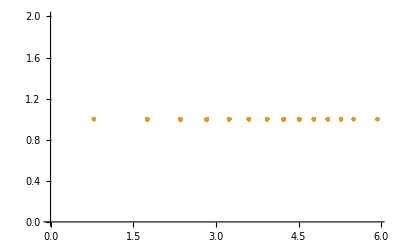

```mathematica
ListPlot[{ToPlotZ0Analytic,ToPlotZ0from𝒜ℬ}]
```

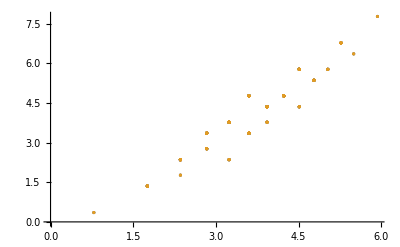

```mathematica
ListPlot[{ToPlotM0Analytic,ToPlotM0from𝒜ℬ}]
```

Exporting Z and M to be plotted outside of Mathematica. The first column is the norm of the momentum and the second column the values of either Z or M, as indicated.

```mathematica
(*Automatizing the exporting of the results*)
```

```mathematica
MZDirectory=FileNameJoin[{NotebookDirectory[],"MZ"}];
IdentifierString="_Nxyz_"<>ToString[Nxyz]<>"_Nt_"<>ToString[Nt]<>"_kappa_"<>ToString[NumberForm[κ,6]]<>".txt";
ExportMZ[name_String,datatoexport_]:=Export[FileNameJoin[{MZDirectory,name<>IdentifierString}],datatoexport,"Table"];
```

```mathematica
ExportMZ@@@{{"Z0Formula",ToPlotZ0from𝒜ℬ},{"Z0Analytic",ToPlotZ0Analytic},{"M0Formula",ToPlotM0from𝒜ℬ},{"M0Analytic",ToPlotM0Analytic}};
```

### Improved Propagator SI

```mathematica
Clear[𝒜I0,ℬI0,AI0from𝒜ℬ,BI0from𝒜ℬ]
```

Improved Propagator as defined in hep-lat/0007028. the “I” propagator can be obtained from the naive propagator.

```mathematica
SI0[ap_,a_,b_]:=(1.+am[κ]) S0[ap,a,b]-1/2. IdentityMatrix[4] a,b
```

Again auxiliary functions to obtain Z and M from the traces of the propagator

```mathematica
𝒜I0[ap_]:=I/(4*3*aksqrd[ap]) Sum[Tr[SI0[ap,a,a].akslash[ap]],{a,1,3}]
```

```mathematica
ℬI0[ap_]:=1/(4*3)Sum[Tr[SI0[ap,a,a]],{a,1,3}]
```

```mathematica
AI0from𝒜ℬ[ap_]:=𝒜I0[ap]/(aksqrd[ap]𝒜I0[ap]^2+ℬI0[ap]^2)
BI0from𝒜ℬ[ap_]:=ℬI0[ap]/(aksqrd[ap]𝒜I0[ap]^2+ℬI0[ap]^2)
```

Improved ZI and MI functions

```mathematica
ZI0from𝒜ℬ[ap_]:=1/AI0from𝒜ℬ[ap]
MI0from𝒜ℬ[ap_]:=BI0from𝒜ℬ[ap]/AI0from𝒜ℬ[ap]
```

```mathematica
ToPlotZI0from𝒜ℬ=(({Norm[#],ZI0from𝒜ℬ[#]})&/@Momenta);
```

```mathematica
ToPlotMI0from𝒜ℬ=(({Norm[#],MI0from𝒜ℬ[#]})&/@Momenta);
```

Analytic Formulas for ZI and MI are also available in the free case

```mathematica
d[ap_]:=aksqrd[ap]+(am[κ]+1/2 akhatsqrd[ap])^2
a4Δksqrd[ap_]:=akhatsqrd[ap]-aksqrd[ap]
BIprime[ap_]:=am[κ]+(am[κ])^2/2+a4Δksqrd[ap]/2-akhatsqrd[ap]^2/8
```

```mathematica
ZI0Analytic[ap_]:=((aksqrd[ap])(1+am[κ])^2+BIprime[ap]^2)/((1+am[κ])d[ap])
```

```mathematica
MI0Analytic[ap_]:=-1/2(am[κ]^2-a4Δksqrd[ap]+(akhatsqrd[ap])^2/4)/(1+am[κ])+am[κ]
```

```mathematica
ToPlotZI0Analytic=(({Norm[#],ZI0Analytic[#]})&/@Momenta);
ToPlotMI0Analytic=(({Norm[#],MI0Analytic[#]})&/@Momenta);
```

The plot shows that the results coming from the traces are in agreement with the analytic formulas

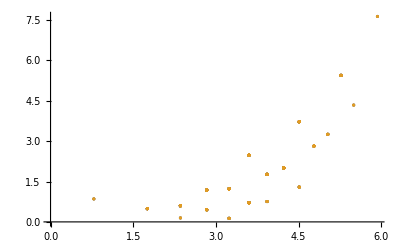

```mathematica
ListPlot[{ToPlotZI0Analytic,ToPlotZI0from𝒜ℬ}]
```

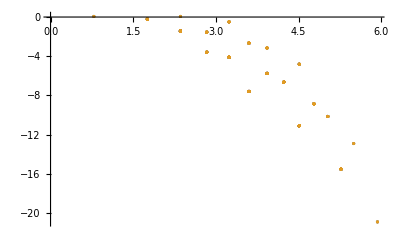

```mathematica
ListPlot[{ToPlotMI0from𝒜ℬ,ToPlotMI0Analytic}]
```

Exporting ZI and MI to be plotted outside of Mathematica. The first column is the norm of the momentum and the second column the values of either ZI or MI, as indicated.

```mathematica
ExportMZ@@@{{"ZI0Formula",ToPlotZI0from𝒜ℬ},{"ZI0Analytic",ToPlotZI0Analytic},{"MI0Formula",ToPlotMI0from𝒜ℬ},{"MI0Analytic",ToPlotMI0Analytic}};
```

## Comparison with C code

C code is inverting the matrix with BiCGStab algorithm.

```mathematica
(*The result from C code is printing all components of the momentum and then Z0, M0, ZI0,MI0 in this order. Needs a conversion to compare with the previous plots.*)
ResultFromC=Insert[Take[#,-4],Norm[Take[#,4]],1]&/@Import[FileNameJoin[{MZDirectory,"MZFree"<>IdentifierString}],"Table"];
```

```mathematica
ToPlotZ0FromC=ResultFromC[[All,{1,2}]];
ToPlotM0FromC=ResultFromC[[All,{1,3}]];
ToPlotZI0FromC=ResultFromC[[All,{1,4}]];
ToPlotMI0FromC=ResultFromC[[All,{1,5}]];
```

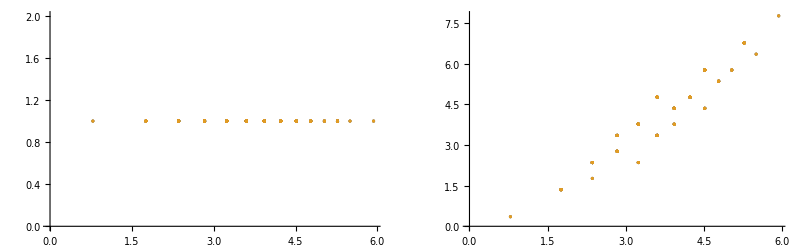
Comparing Analytic Result with produced by C code for Naïve Free Propagator
-Graphics-

```mathematica
Column[{"Comparing Analytic Result with produced by C code for Naïve Free Propagator",GraphicsRow[{ListPlot[{ToPlotZ0Analytic,ToPlotZ0FromC}],ListPlot[{ToPlotM0Analytic,ToPlotM0FromC}]}]}]
```

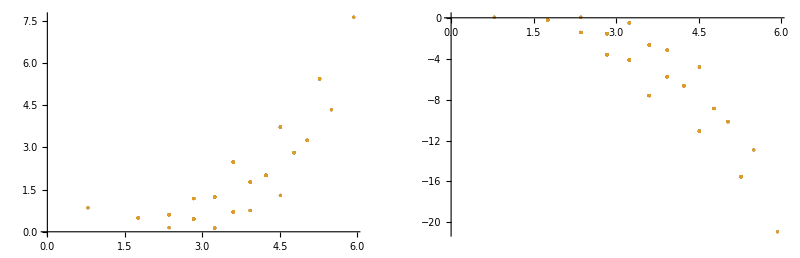
Comparing Analytic Result with produced by C code for Improved Free Propagator
-Graphics-

```mathematica
Column[{"Comparing Analytic Result with produced by C code for Improved Free Propagator",GraphicsRow[{ListPlot[{ToPlotZI0Analytic,ToPlotZI0FromC}],ListPlot[{ToPlotMI0Analytic,ToPlotMI0FromC}]}]}]
```

Residues (Difference between result obtained by C code and analytical formulas)

```mathematica
Residues=Insert[Take[#,-4]-Through[{Z0Analytic,M0Analytic,ZI0Analytic,MI0Analytic}[Take[#,4]]],Norm[Take[#,4]],1]&/@Import[FileNameJoin[{MZDirectory,"MZFree"<>IdentifierString}],"Table"];
```

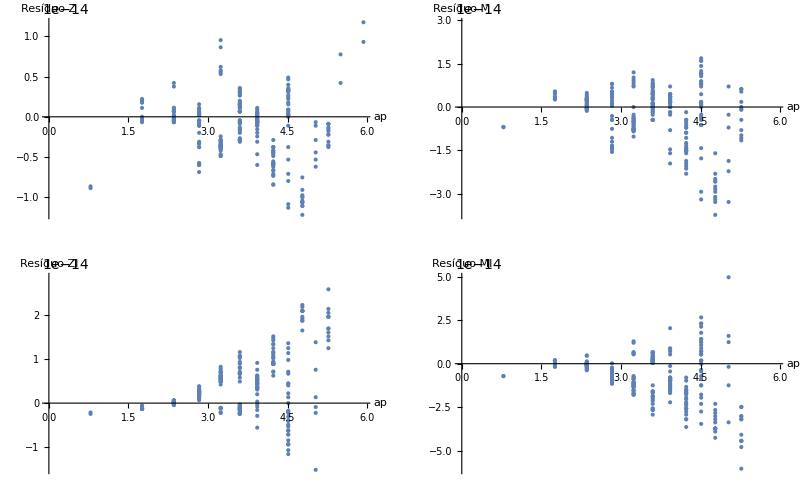

```mathematica
GraphResidues=GraphicsGrid[Partition[ListPlot[#[[1]],AxesLabel->{"ap","Resíduo "<>#[[2]]},LabelStyle->{Black}]&/@Transpose[{Table[Residues[[All,{1,i}]],{i,2,5}],{"Z","M","ZI","MI"}}],2],Frame->All]
```

```mathematica
MaximumResidueAbsValue=(If[+##>0,##]&@@{Max[#],Min[#]}&)/@(Residuesᵀ[[2;;5,All]])
```

{-1.22125×10^-14,1.19016×10^-13,1.58984×10^-13,-4.12115×10^-13}